```mathematica
ClearAll[x,y, η, ω, t, ϕ, R,a, b] 
$Assumptions =0<=x&& ξ >=0&& t<=Pi/2&& 0 <= a <= 1 && 0 <= b <= 1;
R = { { a, -b}, {b, a} };
ω = 1;
Solve[ξ== R[[1]].{x, Sqrt[x]}, x];
xrule = Simplify[%/.{a->Cos[ω t], b->Sin[ω t]}];
(a √x+b x)/.{a->Cos[ω t], b->Sin[ω t]};
%/.xrule;
Simplify[%]//First
ηplus = Piecewise[{{Sqrt[ξ],t==0},{-ξ^2,t==Pi/2}},%]
```

1/2 Tan[t] (2 ξ+Sec[t] √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Sin[t] Tan[t])+(Cos[t] √(2 ξ Sec[t]+Sec[t]^2 √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Tan[t]^2))/(√2)

Piecewise[{{√ξ, t==0}, {-ξ^2, t==π/2}, {1/2 Tan[t] (2 ξ+Sec[t] √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Sin[t] Tan[t])+(Cos[t] √(2 ξ Sec[t]+Sec[t]^2 √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Tan[t]^2))/(√2), True}}]

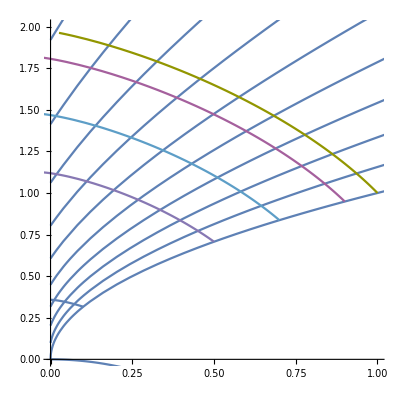

```mathematica
Show[Table[
ParametricPlot[
Evaluate[{ξ,ηplus}/.{t->τ}],
 {ξ, 0, 2},
PlotRange->{{0,1},{0,2}}
],
 {τ, 0, Pi/2, Pi/32}
],
ParametricPlot[Evaluate[{ξ[t],η[t]}/.sol],{t, 0, .5},PlotRange->{{0,2},{0,2}}],
AspectRatio->1
]
```

```mathematica
ϕ[ξ_, η_, t_] = η - ηplus//Simplify
```

η-(Piecewise[{{1/2 Tan[t] (2 ξ+Sec[t] √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Sin[t] Tan[t])+(Cos[t] √(2 ξ Sec[t]+Sec[t]^2 √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Tan[t]^2))/(√2), 2 t≠π}, {-ξ^2, True}}])

```mathematica
dϕ = FullSimplify[Flatten[D[ϕ[ξ,η,t],{{ξ,η}}]]]
```

{-(Piecewise[{{Tan[t]+(Abs[Sin[t]] Tan[t])/(√(4 ξ Cos[t]+Sin[t]^2))+(Abs[Sin[t]]+√(4 ξ Cos[t]+Sin[t]^2))/(√(1+8 ξ Cos[t]-Cos[2 t]) √(2 ξ Sec[t]+Abs[Sin[t]] Sec[t]^2 √(4 ξ Cos[t]+Sin[t]^2)+Tan[t]^2)), 2 t≠π}, {-2 ξ, True}}]),1}

```mathematica
%/.{t->0}
```

{-1/(2 √ξ),1}

```mathematica
ϕt=((3+Cos[2 t]) Sec[t]^2 √Sin[t] (2 ξ+Abs[Sin[t]] Sec[t] √(4 ξ Cos[t]+Sin[t]^2)+Sin[t] Tan[t]))/(4 √(4 ξ Cos[t]+Sin[t]))+1/2 Sec[t]^2 (2 ξ+Sec[t] √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Sin[t] Tan[t])-(Sin[t] √(2 ξ Sec[t]+Sec[t]^2 √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Tan[t]^2))/(√2)+(ξ 2Cos[t]+Sec[t] (3 ξ Sin[t]^2+(ξ+Sec[t]) √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Sin[t] Tan[t]))/(√2 √(4 ξ Cos[t] +Sin[t]^2)√(2 ξ Sec[t]+Sec[t]^2 √(4 ξ Cos[t] Sin[t]^2+Sin[t]^4)+Tan[t]^2));
```

```mathematica
{v1, v2} = dϕ ϕt;
```

```mathematica
{v1t, v2t} = {v1,v2}/.{ξ->ξ[t], η->η[t]};
sol = 
Table[
Flatten[NDSolve[ { ξ'[t] == v1t , η'[t] == v2t , ξ[0] == ξ0, η[0] == Sqrt[ξ[0]]}, {ξ, η}, {t, 0, Pi/2-Pi/32}]],
{ξ0, .1, 1,.1}
]
```

NDSolve::ndsz: At t == 0.064694, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.146072, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.220142, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]},{ξ→InterpolatingFunction[…],η→InterpolatingFunction[…]}}

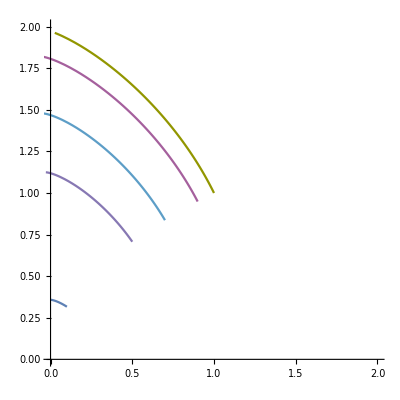

```mathematica
ParametricPlot[Evaluate[{ξ[t],η[t]}/.sol],{t, 0, .5},PlotRange->{{0,2},{0,2}}]
```